Created by: jacobm on 12-19-2017 20:20:21

### Categorization

Symbol

Synonyms

### Keywords

### Syntax Templates

Details

Security Details

"   Potential security risk"

# QuantumDiscreteState

QuantumFiniteDimensionalState[{spec_1, spec_2, …,  spec_n}]
yields the finite dimensional quantum state resulting from taking the tensor product of the states specified by spec_i.

## Tutorials

Related Demonstrations

## Related Links

## See Also

## More About

Autogenerated

## Examples | More Examples ⊳

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a two-level quantum system, or "qubit", in the "0" computational basis state:

```mathematica
QuantumFiniteDimensionalState[{ {"BasisState", {0}}}]
```

QuantumFiniteDimensionalState[…]

View the qubit on the Bloch Sphere:

```mathematica
%["BlochPlot"]
```

-Graphics3D-

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Initialize a 3-qubit register in the "4" number state:

```mathematica
reg = QuantumFiniteDimensionalState[{{"QuantumRegister", 3, 4}}]
```

QuantumFiniteDimensionalState[…]

```mathematica
reg["StateVector"]//MatrixForm
```

(0
0
0
0
1
0
0
0)

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Generate a random pure state for a five-level quantum system:

```mathematica
s = QuantumFiniteDimensionalState[{{"RandomPure", 1}}, "QuditDimension" -> 5]
```

QuantumFiniteDimensionalState[…]

Plot its amplitudes and relative phases:

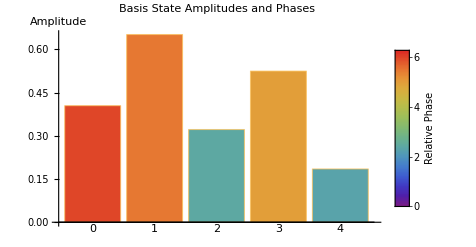

```mathematica
s["Plot"]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Generate a product state of two three level quantum systems:

```mathematica
qstate = QuantumFiniteDimensionalState[{ {1, 0, ⅈ},  {1, 1, 0}}, "QuditDimension" -> 3]
```

QuantumFiniteDimensionalState[…]

View its state vector:

```mathematica
%["StateVector"]//Normal//MatrixForm
```

(1/2
1/2
0
0
0
0
ⅈ/2
ⅈ/2
0)

Trace out the first subsystem

```mathematica
reducedState = QuantumPartialTr[qstate, {1}]
```

QuantumFiniteDimensionalState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a Bell state for two qubits:

```mathematica
bell = QuantumFiniteDimensionalState[{"PhiPlus"}]
```

QuantumFiniteDimensionalState[…]

Verify the two subsystems are entangled:

```mathematica
QuantumEntangledObjectsQ[bell, {{1}, {2}}]
```

True

Query for the ordering of basis states in the state vector:

```mathematica
bell["BasisStates"]
```

{00,01,10,11}

## More Examples

### Scope

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Specify the dimension of the quantum system:

```mathematica
QuantumFiniteDimensionalState[{"PureUniformSuperposition"}, "QuditDimension" -> 4]
```

QuantumFiniteDimensionalState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Specify combined basis states:

```mathematica
qstate = QuantumFiniteDimensionalState[{ {"BasisState", {1, 0,1}}}]
```

QuantumFiniteDimensionalState[…]

```mathematica
qstate["StateVector"]//MatrixForm
```

(0
0
0
0
0
1
0
0)

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Numerically specified quantum states are automatically normalized:

```mathematica
QuantumFiniteDimensionalState[{ {1,2}}]
```

QuantumFiniteDimensionalState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Entangled states may be input by listing entries in the canonical order in the combined basis:

```mathematica
QuantumFiniteDimensionalState[{{α,β,γ, δ}}]
```

QuantumFiniteDimensionalState[…]

```mathematica
%["BasisStates"]
```

{00,01,10,11}

### Generalizations & Extensions

### Options

### Applications

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Generate qubits in basis states of alternative bases:

```mathematica
left = QuantumFiniteDimensionalState[{ "Left"}]
```

QuantumFiniteDimensionalState[…]

```mathematica
right = QuantumFiniteDimensionalState[{ "Right"}]
```

QuantumFiniteDimensionalState[…]

```mathematica
plus = QuantumFiniteDimensionalState[{"Plus"}]
```

QuantumFiniteDimensionalState[…]

```mathematica
minus = QuantumFiniteDimensionalState[{"Minus"}]
```

QuantumFiniteDimensionalState[…]

Plot all four on the Bloch Sphere:

```mathematica
QuantumBlochPlot[{left, right, plus, minus}, PlotStyle -> {Red, Yellow, Blue, Green}]
```

-Graphics3D-

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Generate all four Bell states:

```mathematica
phiP = QuantumFiniteDimensionalState[{ "PhiPlus"}]
```

QuantumFiniteDimensionalState[…]

```mathematica
phiM = QuantumFiniteDimensionalState[{ "PhiMinus"}]
```

QuantumFiniteDimensionalState[…]

```mathematica
psiP = QuantumFiniteDimensionalState[{ "PsiPlus"}]
```

QuantumFiniteDimensionalState[…]

```mathematica
psiM = QuantumFiniteDimensionalState[{ "PsiMinus"}]
```

QuantumFiniteDimensionalState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a four-qubit W-state

```mathematica
w = QuantumFiniteDimensionalState[{{"W", 4}}]
```

QuantumFiniteDimensionalState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a three-qubit GHZ state:

```mathematica
ghz = QuantumFiniteDimensionalState[{ "GHZ"}]
```

QuantumFiniteDimensionalState[…]

Plot its amplitudes:

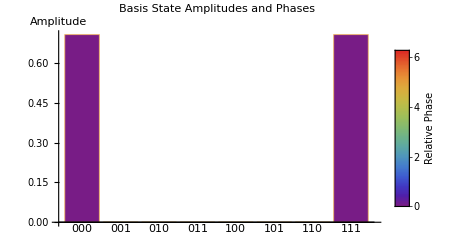

```mathematica
ghz["Plot"]
```

Tracing out subsystems of a pure state can result in a mixed state

```mathematica
sReduced = QuantumPartialTr[ghz, {1}]
```

QuantumFiniteDimensionalState[…]

```mathematica
sReduced["Purity"]
```

1/2

### Properties & Relations

### Possible Issues

### Interactive Examples

### Neat Examples

Design Discussion

Application Notes

Test Cases

Function Essay